# L2DT (Lensing with Large Deviation Theory)

### Author

This notebook was written by Alexandre Barthelemy -- Universitäts-Sternwarte München, Fakultät für Physik der Ludwig-Maximilians-Universität -- in 2023. I write it as a pedagogical introduction to the computation of the lensing PDFs in large deviation theory.
Any questions/remarks should be addressed to A.Barthelemy@lmu.de

### Content

This Mathematica notebook presents a practical and pedagogical implementation of the weak-lensing convergence/aperture mass PDFs as computed with the large-deviations formalism.
You are free to use this notebook for your own science. If you do so please cite arXiv:2307.09468.

Currently it computes:
- The convergence cumulant generating function (CGF) and 1-point PDF for single source planes as well as source distributions.
- New lensing kernels when using the BNT transform, a nulling technique to compartmentalise small-scales physics to the closest sources in a tomographic experiment.
- The joint CGFs and joint PDFs between projected quantities for any projection kernel. This allows to compute joint statistics between different lensing sources and/or lensing and clustering quantities.
- The correction induced by the Kaiser-Squires reconstruction of the convergence field from a masked shear field.
- The aperture-mass CGF and 1-point PDF for single source planes as well as source distributions.

The notebook restricts itself to the case of top-hat filters although the theory allows for more general filters. It also ignores simulation-specific corrections (like discrete lensing shells or resolution effects) that are usually necessary for fair comparison of the formalism to simulated data. It assumes one specific cosmology since the goal of this notebook is mostly pedagogical but which is straightforwardly changed in the notebook itself.

Later revisions of this notebook will include :
- Inclusion of observational systematics (baryonic feedback, intrinsic alignments, photometric redshift errors) and high-order lensing corrections (lens-lens couplings, geodesic deviation, reduced shear and magnification bias).
- More general filtering scheme.

## I) The Convergence CGF/PDF

```mathematica
ClearAll["Global`*"];
```

## Non - linear "2D variance" along the line-of-sight

The two following cells don’t need to be re-evaluated since I have saved their results. They would have to be re-run for a different cosmology but they are independent of the projection kernels and the angular scales we are looking at.

#### non - linear matter power spectrum (uncomment to run)

```mathematica
(*

(*We first load the non-linear power spectrum obtained with Class*)
ks=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/dataconfig_ks.dat"}],Number,RecordLists->True]//Flatten;
{kmini,kmaxi}={ks[[1]],ks[[-1]]};
zss=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/dataconfig_zs.dat"}],Number,RecordLists->True]//Flatten;
pks=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/fiducial_pks_nl_mm.dat"}],Number,RecordLists->True];
nbz = zss//Length;
nby = ks//Length;

(*We interpolate the power spectrum*)
Pk=Table[{{zss[[a]],ks[[b]]},pks[[a,b]]},{a,1,nbz},{b,1,nby}]//Flatten[#,1]&//Interpolation;

(*We define the 2D top-hat function in fourier space*)
W[l_]=2 BesselJ[1,l]/(l);

(*We define the variance at redshift z of a 2D slice of radius R*)
ssigma2[R_,z_]:=NIntegrate[Pk[z,k] k W[k*R]^2,{k,kmini,kmaxi},Method->{"GlobalAdaptive","SymbolicProcessing"->0,"MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->16,PrecisionGoal->7,AccuracyGoal->Infinity]/2/Pi //Quiet;

(*We compute it on a number of nodes. We will interpolate it but let's not do it at this stage to avoid numerical interpolation issues 
that could for example happen for a bad choice of interpolation degree*)
(*The range of R values needs to be adapted to the redshift of sources and chosen angular top-hat radii*)
sigm2=ParallelTable[{{R,z},ssigma2[R,z]},{R,0.0001,30,0.025},{z,0,5,0.25}]//Flatten[#,1]&;

(*Since this entire cell operation is lengthy and only depends on the cosmology, we can save it and re-use it later*)
Export[FileNameJoin[{NotebookDirectory[],"halofit_variance.m"}],sigm2]

*)
```

#### linear matter power spectrum (uncomment to run)

```mathematica
(*

(*We load the linear power spectrum at z = 0 (or any z for that matter) obtained with Class*)
(*The kappa PDF is independent of the redshift evolution of the linear spectrum (growth factor) as is apparent in the definition of the 2D rate function*)

ks=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/dataconfig_ks.dat"}],Number,RecordLists->True]//Flatten;
{kmini,kmaxi}={ks[[1]],ks[[-1]]};
pks=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/fiducial_pks_mm.dat"}],Number,RecordLists->True];
Pk={ks,pks}//Transpose//Interpolation;
W[l_]=2 BesselJ[1,l]/(l);
ssigma2[R_]:=NIntegrate[Pk[k] k W[k*R]^2,{k,kmini,kmaxi},Method->{"GlobalAdaptive","SymbolicProcessing"->0,"MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->16,PrecisionGoal->7,AccuracyGoal->Infinity]/2/Pi //Quiet;
sigm2=ParallelTable[{R,ssigma2[R]},{R,0.00001,50,0.25}];  
Export[FileNameJoin[{NotebookDirectory[],"linear_variance.m"}],sigm2]

*)
```

#### Projected variance

The modelling of the non-linear variance is crucial to the accuracy of the PDF . It is also a good sanity check to later recover the projected variance from the PDF we will have computed . Thus let us here compute the value of the non-linear projected variance (the variance of the convergence field smoothed at some scale).

InterpolatingFunction[…]

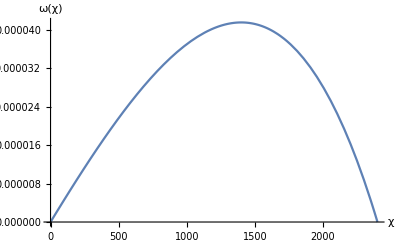

The variance of the κ field in a top-hat of radius 20 arcmin and the above lensing kernel is: 0.0000291131

```mathematica
(*We start by importing the non-linear line-of-sight variance we have computed above, and interpolate it (degree 3 by default)*)
sigm2= Import[FileNameJoin[{NotebookDirectory[],"halofit_variance.m"}]];
sig2=sigm2//Interpolation

(*We formally define the cosmology that needs to be the same as the one used for the power spectrum. 
We need it for the lensing/projection kernel*)
Omegam = 0.279;
Omegal = 1-Omegam;
H0 = 100;  (*Forces units to Mpc/h. If you edit this notebook make sure that everything is still consistent with that choice.*)
c = 299792.458;

(*Let us define the radius of the angular top-hat radius in radians*)
θ = 0.00581776; (*20 arcmin*)

(*Let us define the radial comoving distance (Mpc/h) as a function of redshift and the cosmological parameters*)
R = Import[FileNameJoin[{NotebookDirectory[],"distance.m"}]];

(*We can also define its opposite, that is the redshift as a function of the comoving distance and the cosmology.
We define both R and zR to illustrate that one can do the integration either in redshift or in comoving distance with the proper jacobian*)
zR= Interpolation[Table[{NIntegrate[(c/H0)/Sqrt[Omegal+Omegam(1+zp)^3],{zp,0,z},PrecisionGoal->15],z},{z,0,6.,0.01}],InterpolationOrder->7];

(*Define here the lensing kernel. We will use with a simple source plane located at redshift zs = 1.0334. 
Note that taking into account more realistic source bins (rather than planes) only changes the projection/lensing kernel. See an example in the BNT transform section of this notebook*)
zs = 1.0334;
Rs=R[zs];
F[Ru_]:=F[Ru]=1.5*Omegam*(H0/c)^2*Ru*(Rs-Ru)/Rs*(1+zR[Ru]);
Plot[F[r],{r,0,Rs},AxesLabel->{"χ","ω(χ)"}]

(*Finally we use the projection formula to obtain the non-linear convergence variance. Here we do the integral in comoving distance rather than redshift*)
Rsamp = 10; (*Sampling for the line-of-sight integral in Mpc/h using Simpson's rule*)
imax = (Rs+Rsamp*0.5)/Rsamp//IntegerPart; (*This makes sure that the last point is below Rs since the definition of the lensing kernel should take into account an heaviside function to make it 0 beyond this value.*)

Rpts = Table[Rsamp*(i−0.5),{i,1,imax}];
nbz=Rpts//Length;
Rweight = Table[Rsamp,{i,1,imax}];

Print["The variance of the κ field in a top-hat of radius 20 arcmin and the above lensing kernel is: ",Table[Rsamp*F[Rsamp*(i−0.5)]^2*sig2[Rsamp*(i−0.5)*θ,zR[Rsamp*(i−0.5)]],{i,1,imax}]//Total]
```

## Computing the Convergence Cumulant Generating Function along the line-of-sight

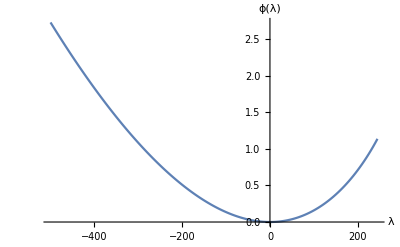

{{-500,2.7276},{-495,2.67931},{-490,2.63136},{-485,2.58376},{-480,2.5365},{-475,2.48958},{-470,2.44302},{-465,2.3968},{-460,2.35094},{-455,2.30543},{-450,2.26028},{-445,2.21548},{-440,2.17105},{-435,2.12698},{-430,2.08327},{-425,2.03993},{-420,1.99696},{-415,1.95436},{-410,1.91213},{-405,1.87028},{-400,1.8288},{-395,1.78771},{-390,1.74699},{-385,1.70667},{-380,1.66672},{-375,1.62717},{-370,1.58801},{-365,1.54924},{-360,1.51087},{-355,1.4729},{-350,1.43533},{-345,1.39816},{-340,1.3614},{-335,1.32505},{-330,1.28911},{-325,1.25358},{-320,1.21847},{-315,1.18378},{-310,1.14952},{-305,1.11568},{-300,1.08226},{-295,1.04928},{-290,1.01674},{-285,0.984627},{-280,0.952957},{-275,0.92173},{-270,0.89095},{-265,0.860619},{-260,0.83074},{-255,0.801318},{-250,0.772355},{-245,0.743854},{-240,0.715818},{-235,0.688252},{-230,0.661159},{-225,0.634542},{-220,0.608405},{-215,0.582751},{-210,0.557585},{-205,0.532909},{-200,0.508728},{-195,0.485046},{-190,0.461866},{-185,0.439192},{-180,0.417029},{-175,0.395381},{-170,0.374251},{-165,0.353644},{-160,0.333565},{-155,0.314018},{-150,0.295007},{-145,0.276536},{-140,0.258612},{-135,0.241237},{-130,0.224417},{-125,0.208157},{-120,0.192462},{-115,0.177337},{-110,0.162787},{-105,0.148817},{-100,0.135432},{-95,0.122639},{-90,0.110443},{-85,0.0988482},{-80,0.087862},{-75,0.0774898},{-70,0.0677376},{-65,0.0586116},{-60,0.0501179},{-55,0.0422631},{-50,0.0350536},{-45,0.0284962},{-40,0.0225977},{-35,0.0173649},{-30,0.0128052},{-25,0.00892569},{-20,0.00573395},{-15,0.00323759},{-10,0.00144444},{-5,0.000362503},{0,-1.52712×10^-29},{5,0.000365343},{10,0.00146716},{15,0.0033143},{20,0.00591586},{25,0.00928114},{30,0.0134197},{35,0.0183415},{40,0.0240565},{45,0.0305752},{50,0.0379082},{55,0.0460667},{60,0.0550619},{65,0.0649057},{70,0.0756099},{75,0.0871872},{80,0.0996504},{85,0.113013},{90,0.127288},{95,0.142491},{100,0.158635},{105,0.175737},{110,0.193813},{115,0.212878},{120,0.232949},{125,0.254046},{130,0.276186},{135,0.299389},{140,0.323676},{145,0.349067},{150,0.375585},{155,0.403254},{160,0.432097},{165,0.462143},{170,0.493417},{175,0.525949},{180,0.559771},{185,0.594915},{190,0.631417},{195,0.669316},{200,0.708653},{205,0.749472},{210,0.791824},{215,0.835762},{220,0.881347},{225,0.92865},{230,0.97775},{235,1.02874},{240,1.08175},{245,1.13693}}

```mathematica
(*Cylindrical collapse parametrisation*)
ζ[x_]=(1-x/ν)^(-ν);
τ[y_]=Module[{x},x/.Solve[y==ζ[x],x][[1]]//Quiet];
ν = 1.4;

(*Load the previously computed non-linear and linear variances*)
sig2ml = Import[FileNameJoin[{NotebookDirectory[],"linear_variance.m"}]];
sig2l=sig2ml//Interpolation;

(*The 2D rate function*)
ψ[δ_,Ru_]=1/2*τ[1+δ]^2*sig2l[Ru*θ]/sig2[Ru*θ,zR[Ru]]/sig2l[(1+δ)^(1/2)*Ru*θ];
dψ[δ_,Ru_]=D[ψ[δ,Ru],{δ,1}];
ddψ[δ_,Ru_]=D[ψ[δ,Ru],{δ,2}];

(*Computation of the projected non-linear CGF along the real axis for points in ypts*)
Clear[deltaintermediate,ϕprojintermediatey]

ymax = 245; (*Be careful that this value does not exceed the critical point (see section on joint PDFs for more detail and practical computation)*)
ymin = -500;
samp = 5;
ypts = Table[y,{y,ymin,ymax,samp}];

deltaintermediate[1,k_]:=delta/.FindRoot[dψ[delta,Rpts[[k]]] - ypts[[1]]*F[Rpts[[k]]],{delta,0},MaxIterations->100]
nby=ypts//Length;
deltaintermediate[n_,k_]:= deltaintermediate[n,k]= delta/.FindRoot[dψ[delta,Rpts[[k]]] - ypts[[n]]*F[Rpts[[k]]],{delta,deltaintermediate[n-1,k]},MaxIterations->100];
deltapts =Table[Table[deltaintermediate[nn,kk],{nn,1,nby}],{kk,1,nbz}]//Transpose;
ϕprojintermediatey[ni_]:= ϕprojintermediatey[ni]= Total[Rweight*(ypts[[ni]]*F[Rpts]*deltapts[[ni]]-ψ[deltapts[[ni]],Rpts])];
ϕprojyREAL = Table[ϕprojintermediatey[nn],{nn,1,nby}];

ListLinePlot[{ypts,ϕprojyREAL}//Transpose,AxesLabel->{"λ","ϕ(λ)"}]
phi = {ypts,ϕprojyREAL}//Transpose
```

```mathematica
f=Interpolation[phi,InterpolationOrder->7]; (*Let's compute the values of the first few cumulants*)
f''[0] (*We check that it's the same number as the previously computed non-linear convergence variance*)
f'''[0]
f''''[0]
```

0.0000291131

6.81594×10^-8

3.41093×10^-10

The CGF is an observable on its own so that we could stop the computation of the 1 - point statistics of the convergence field here. However the PDF is more often used and so we compute it in the next section from the CGF

## Computation of the PDF from the effective collapse approach (see section 2.6 in this paper for details)

```mathematica
ph = {ypts,ϕprojyREAL}//Transpose//Interpolation;
dph[x_]=D[ph[x],{x,1}];
tabledph=dph[ypts];
varphi= ph[ypts];

data= {Sign[ypts]*Sqrt[2*(ypts*tabledph-varphi)],tabledph}//Transpose;
degree=7;
basis=Table[x^k,{k,1,degree}];
zetabis=Fit[data,basis,x]
zeta[x_]=zetabis;
```

0.00539566 x+0.000390198 x^2+0.0000340556 x^3+4.38104×10^-6 x^4+7.91843×10^-7 x^5+1.42324×10^-7 x^6+1.44602×10^-8 x^7

```mathematica
(*Check that the first term squared gives back the variance*)
0.005395656281409012^2
```

0.0000291131

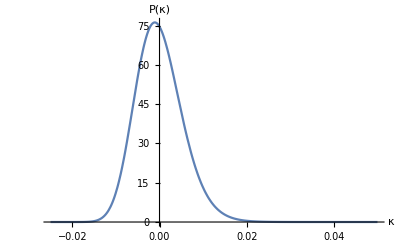

```mathematica
dzeta[t_]=D[zeta[t],{t,1}];

Clear[tauintermediate,taupts,ephi,h,geff];
ymax =2000.;
ymin = 0;
samp=20;
ypts = I*Table[y,{y,ymin,ymax,samp}];

(*The values of ypts might need to be adjusted depending on the computed PDF. 
Plot the imaginary part of yweight*Exp[-ypts*delta]*ephi/Pi for different values of delta (the convergence values) and 
make sure that the sampling and max values are good enough to capture the oscillations and their damping*)

yweight=Append[Prepend[Table[samp I,{a,1,Length[ypts]-2}],samp/2 I],samp/2 I];
nby=ypts//Length;
tauintermediate[1]=tau/.FindRoot[tau-dzeta[tau]*ypts[[1]],{tau,(I 10^(-5))^.5},MaxIterations->1000];
tauintermediate[n_]:= tauintermediate[n]= tau/.FindRoot[tau-dzeta[tau]*ypts[[n]],{tau,tauintermediate[n-1]},MaxIterations->1000];
taupts =Table[tauintermediate[nn],{nn,1,nby}];
ephi= Exp[ypts*zeta[taupts]-taupts^2/2];
h[delta_] := h[delta] = Total[yweight*Exp[-ypts*delta]*ephi/Pi] //Im;
geff = Interpolation[Table[{delta,h[delta]},{delta,-0.08,0.25,.001}]];

Plot[geff[x],{x,-0.025,0.05},AxesLabel->{"κ","P(κ)"}]
```

```mathematica
(*Let's check that we recover the correct variance as a check that the integration was succesful*)
NIntegrate[x^2*geff[x],{x,-0.025,0.05}]-(NIntegrate[x*geff[x],{x,-0.025,0.05}])^2
```

0.0000291131

### A technical comment

A comment on the inverse Laplace transform. We have to perform the following integration:

```mathematica
P(κ)==∫_(-i∞)^(+i∞) dλ/(2πi)(e^(-λκ+ϕ(λ))).
```

Since the result of this integral has to be a real number, we only care about

```mathematica
ℜ[e^(-iλκ+ϕ(iλ))]==e^a·cos(b)
```

with

```mathematica
a==∑_(n==1) (-1)^n Subscript[⟨κ^(2n)⟩, c] λ^(2n)/((2n)!)
```

```mathematica
b==λ(⟨κ⟩-κ)+∑_(n==1) (-1)^n Subscript[⟨κ^(2n+1)⟩, c](λ^(2n+1)/((2n+1)!)).
```

Given the parity of the cosine function this means that if we perform the first integral along the imaginary axis we can just compute ϕ(i λ) for real positive λ values and we have

```mathematica
P(κ)==ℜ[∫_0^(+∞) dλ/π e^(-iλκ+ϕ(iλ))]
```

which is numerically more efficient to implement while discarding the imaginary part.

## Appendix : Use of the BNT transform (originally introduced in arXiv:1312.0430)

The BNT transform is in essence just a change in the lensing kernel neglecting geodesic deviation, lens - lens couplings and more generally any non-linear corrections to the standard convergence definition as a line-of-sight projection of the  density contrast.

0.410569

-1.41057

1

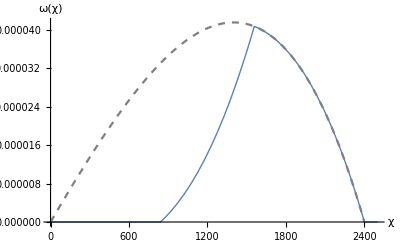

```mathematica
(*For source planes*)

z1=0.3;
z2=0.6;
z3=1.0334;  (*For pedagogical reasons I've chosen the 3rd plane to be our previous source plane so as to compare the new BNT kernel to the standard one*)

R1=R[z1];
R2=R[z2];
R3=R[z3];

cf[i_,j_,k_]=R[i]*(R[j]-R[k]);
p1=cf[z1,z2,z3]/cf[z3,z1,z2]
p2=cf[z2,z3,z1]/cf[z3,z1,z2]
p3=1

Fnull[Ru_]=Piecewise[{{1.5*Omegam*(H0/c)^2*p1*Ru^2*(1/R1-1/Ru)*(1+zR[Ru]),R1≤Ru<R2},{1.5*Omegam*(H0/c)^2*p3*Ru^2*(1/Ru-1/R3)*(1+zR[Ru]),R2≤Ru<R3}}];

Show[Plot[{Fnull[ru]},{ru,0,R3+100},PlotRange->All,AxesLabel->{"χ","ω(χ)"},PlotStyle->Thick],Plot[F[ru],{ru,0,R3},PlotStyle->{Dashed,Gray}]]
```

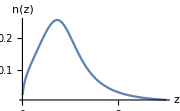
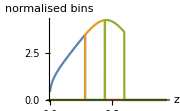

0.118633

-1.11863

1

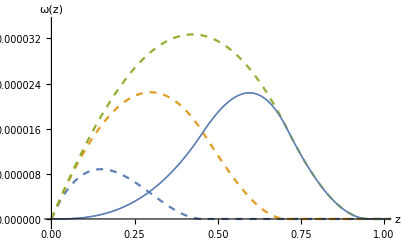

```mathematica
(*For source bins*)

(*Let's define equipopulated source bins from an arbitrary source distribution n(z) -> we switch to redshift rather than comoving distance for simplicity*)
nz = Import[FileNameJoin[{NotebookDirectory[],"realistic_nz.cat"}]]//Interpolation;
norm1 = NIntegrate[nz[z], {z, 0.005, 0.4542}];
norm2 = NIntegrate[nz[z], {z, 0.4542, 0.7075}];
norm3 = NIntegrate[nz[z], {z, 0.7075, 0.9549}];
nz1[z_] = Piecewise[{{nz[z]/norm1, 0.005 <= z < 0.4542}}];
nz2[z_] = Piecewise[{{nz[z]/norm2, 0.4542 <= z < 0.7075}}];
nz3[z_] = Piecewise[{{nz[z]/norm3, 0.7075 <= z < 0.9549}}];

{Plot[nz[z],{z,0.005,3},PlotRange->All,ImageSize->Small,AxesLabel->{"z","n(z)"}],Plot[{nz1[z], nz2[z], nz3[z]}, {z, 0.005, 1.5}, PlotRange -> All,ImageSize->Small,AxesLabel->{"z","normalised bins"}]}

(*We now compute the original lensing kernels for each of the 3 source bins *)
zmin = 10^(-8);
zmax = 3+10^(-8);
zsamp = 0.01;
zpts = Table[z,{z,zmin,zmax,zsamp}];
Fbin[z_,s_]=Piecewise[{{1.5*Omegam*(H0/c)^2*R[z]*(R[s]-R[z])/R[s]*(1+z),z<=s}}]; 
F1 = Table[NIntegrate[nz1[s]*Fbin[z,s],{s,0,3}],{z,zpts}];
F2 = Table[NIntegrate[nz2[s]*Fbin[z,s],{s,0,3}],{z,zpts}];
F3 = Table[NIntegrate[nz3[s]*Fbin[z,s],{s,0,3}],{z,zpts}];

(*We now compute the new BNT weights*)
R1 = 1/NIntegrate[nz1[z]/R[z],{z,0.005,0.4542}];
R2 = 1/NIntegrate[nz2[z]/R[z],{z,0.4542,0.7075}];
R3 = 1/NIntegrate[nz3[z]/R[z],{z,0.7075,0.9549}];

p1 = R1*(R2-R3)/(R3*(R1-R2))
p2 = -1 - p1
p3 = 1

(*Let's plot the result*)
Fbinnull = {zpts,p1*F1+p2*F2+p3*F3}//Transpose;
Show[ListLinePlot[{Fbinnull},PlotRange->{{0,1.},{-0.1*10^(-5),3.5*10^(-5)}},AxesLabel->{"z","ω(z)"},PlotStyle->Thick],ListLinePlot[{{zpts,F1}//Transpose,{zpts,F2}//Transpose,{zpts,F3}//Transpose},PlotRange->All,PlotStyle->{Dashed}],ListLinePlot[{Fbinnull},PlotRange->{{0,1.},{-0.1*10^(-5),3.5*10^(-5)}},AxesLabel->{"z","ω(z)"},PlotStyle->Thick]]
```

## II) Joint PDFs along the line of sight (between lensing and clustering or different lensing sources)

This section was originally written to compute joint convergence (or aperture mass) PDFs between BNT transformed variables and thus focuses on the joint distribution between 2 variables (which can then be used to compute the whole joint PDF between an arbitrary number of BNT transformed variables -- see https://ui.adsabs.harvard.edu/abs/2022PhRvD.105d3537B/abstract ). Nevertheless, the principle of this implementation is straightforwardly extended to the case of more variables albeit becoming more numerically expensive . 

Note moreover that since one can use arbitrary lensing kernels for the two variables separately, one can choose a flat kernel for one variable and thus obtain the joint PDF between some lensing quantity and the matter density contrast. Finally, a linear galaxy bias b1 is taken into account as ϕ_gal(λ) = ϕ_matter (b1 λ). This renders the computation of a joint PDF between galaxy density and lensing identical to the joint lensing PDF between two redshift sources. More involved models for non-linear halo/galaxy bias and consideration of non-poissonian shot-noise in the LDT formalism have been introduced in the literature but will not be shown here.

## Fit effective collapse at each redshift slice

In real space, the computation of ϕ (λ1, λ2) is identical to what we have done for the 1 - pt kappa PDF, literally replacing the terms ωλ (our "ypts[[n]]*F[Rpts[[k]]]" - like terms) by  (ω1 λ1 +  ω2 λ2) . However, the analytic continuation of ϕ (λ1, λ2) to the entire 4D complex plane -- needed for the computation of the joint-PDF via inverse Laplace transform -- cannot be performed in the same way. Since this joint CGF is really a projected 1D CGF in disguise, we thus rather compute the effective collapse coefficients for the 1D CGF of the matter density slices along the line-of-sight which can then be prolonged to complex arguments.

```mathematica
(*To avoid any conflicts between variables of the same names which might have slighlty changed, 
let's clear everything and start from scratch*)
ClearAll["Global`*"];

(*We set the angular scale in radians -- it has to be the same for the two variable*)
θ = 0.00581776; (*20 arcmin*)

(*Load the previously computed non-linear and linear variances*)
sigm2= Import[FileNameJoin[{NotebookDirectory[],"halofit_variance.m"}]];
sig2=sigm2//Interpolation;
sig2ml = Import[FileNameJoin[{NotebookDirectory[],"linear_variance.m"}]];
sig2l=sig2ml//Interpolation;

(*We formally define the cosmology that needs to be the same as the one used for the power spectrum. 
We need it for the lensing/projection kernels and distances definition*)
Omegam = 0.279;
Omegal = 1-Omegam;
H0 = 100;  (*Forces units to Mpc/h. If you edit this notebook \make sure that everything is still consistent with that choice.*)
c = 299792.458;

ζ[x_]=(1-x/ν)^(-ν);
τ[y_]=Module[{x},x/.Solve[y==ζ[x],x][[1]]//Quiet];
ν = 1.4;

(*Let us define the radial comoving distance (Mpc/h) as a function of redshift and the cosmological parameters*)
R = Import[FileNameJoin[{NotebookDirectory[],"distance.m"}]];
zR= Interpolation[Table[{NIntegrate[(c/H0)/Sqrt[Omegal+Omegam(1+zp)^3],{zp,0,z},PrecisionGoal->15],z},{z,0,6.,0.01}],InterpolationOrder->7];

(*The 2D rate function and its derivatives*)
ψ[δ_,Ru_]=1/2*τ[1+δ]^2*sig2l[Ru*θ]/sig2[Ru*θ,zR[Ru]]/sig2l[(1+δ)^(1/2)*Ru*θ];
dψ[δ_,Ru_]=D[ψ[δ,Ru],{δ,1}];
ddψ[δ_,Ru_]=D[ψ[δ,Ru],{δ,2}];
```

Let us find the critical real lambda values after which the 2D rate functions along the line-of-sight are no more strictly convex

310

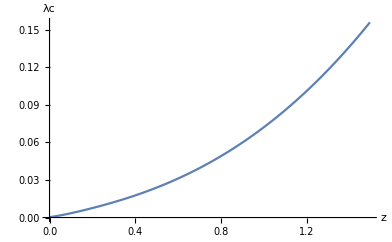

```mathematica
Rsamp = 10; (*Samling of the line-of-sight in Mpc/h*)
Rs = R[1.5]; (*Arbitrary choice for a stopping point, just increase the value if your sources are higher in redshift*)
imax = (Rs+Rsamp*0.5)/Rsamp//IntegerPart; (*This makes sure that the last point is just below Rs*)
Rpts = Table[Rsamp*(i−0.5),{i,1,imax}];
Rweight = Table[Rsamp,{i,1,imax}];
nbz = imax

deltac = Table[delta/.FindRoot[ddψ[delta,Rpts[[k]]],{delta,0.00316},MaxIterations->1000],{k,1,imax}];
lambdac = dψ[deltac,Rpts];

(*Let's plot the values of the critical lambda as a function of redshift along the line-of-sight*)
ListLinePlot[{zR[Rpts],lambdac}//Transpose,AxesLabel->{"z","λc"}]
```

[skip the next cell if you’re only interested in joint PDFs] As an exercise, let’s use the previous plot to compute the critical real lambda value for the projected CGF of the previously computed kappa field at source plane zs = 1.0334:

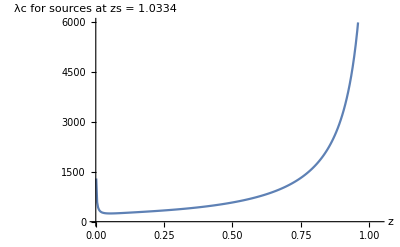

The critical point of the projected CGF (thus taking the kernel into account) is the smallest critical point along the line of sight: 247.779

```mathematica
(*Let's reintroduce the appropriate lensing kernel*)
F[Ru_]=1.5*Omegam*(H0/c)^2*Ru*(R[1.0334]-Ru)/R[1.0334]*(1+zR[Ru]);

ListLinePlot[{zR[Rpts[[;;230]]],lambdac[[;;230]]/F[Rpts[[;;230]]]}//Transpose,AxesLabel->{"z","λc for sources at zs = 1.0334"},PlotRange->{{0,1.0334},{-10,6000}}]
Print["The critical point of the projected CGF (thus taking the kernel into account) is the smallest critical point along the line of sight: ", Min[lambdac[[;;230]]/F[Rpts[[;;230]]]]]
```

Let’s now compute the CGF in each slice up to its critical point

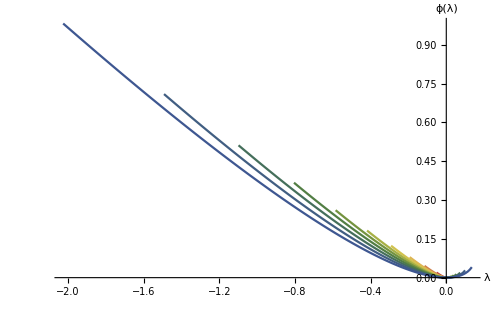

```mathematica
Clear[deltaintermediate,deltapts,ϕz,ymax,samp,ypts]
ymax[k_] := lambdac[[k]] - 0.05*lambdac[[k]]; (*Security measure to avoid stepping on the exact critical value*)
ymin[k_] := -15*ymax[k];
samp[k_] := (ymax[k]-ymin[k])/200;
ypts[k_] := Table[y,{y,ymin[k],ymax[k],samp[k]}];
nby = ypts[1]//Length;
deltaintermediate[1,k_]:=delta/.FindRoot[dψ[delta,Rpts[[k]]] - ypts[k][[1]],{delta,(10^(-5))^.5,-0.9999,6.1},MaxIterations->1000];
deltaintermediate[n_,k_]:= deltaintermediate[n,k]= delta/.FindRoot[dψ[delta,Rpts[[k]]] - ypts[k][[n]],{delta,deltaintermediate[n-1,k],-0.9999,6.1},MaxIterations->1000];
deltapts =Table[Table[deltaintermediate[nn,kk],{nn,1,nby}],{kk,1,nbz}];
ϕz[k_]:={ypts[k],(ypts[k]*deltapts[[k]]-ψ[deltapts[[k]],Rpts[[k]]])}//Transpose;
ϕtablez = Table[ϕz[kk],{kk,1,nbz}];

(*Let's visualise some of these CGFs*)
f=ColorData["DarkRainbow"];
ListLinePlot[Table[ϕz[kk],{kk,Table[i,{i,1,nbz,30}]}],PlotStyle->Table[f[1-i],{i,0,1,30/imax}],PlotRange->All,ImageSize->500,AxesLabel->{"λ","ϕ(λ)"}]

(*It's possible to save that*)
(*Export[FileNameJoin[{NotebookDirectory[],"PhiTableR.m"}],ϕtablez]*)
```

{0.00113187,0.00107527}

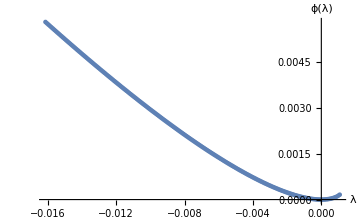
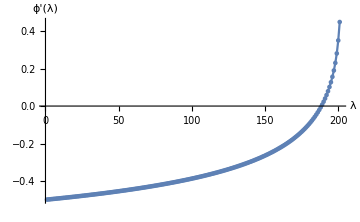

```mathematica
(*A good sanity check consists in looking at the first derivative of the CGFs, especially around the critical point*)
n = 10;
{lambdac[[n]],Max[ypts[n]]}
g = ϕtablez[[n]]//Interpolation;
{Show[ListPlot[ϕtablez[[n]],ImageSize->Medium,AxesLabel->{"λ","ϕ(λ)"}],ListLinePlot[ϕtablez[[n]]]],Show[ListPlot[g'[ypts[n]],PlotRange->All,ImageSize->Medium,AxesLabel->{"λ","ϕ'(λ)"}],ListLinePlot[g'[ypts[n]],PlotRange->All]]}
```

Finally let’s fit effective collapse parameters at each slice (one might want to retain higher degrees than 5 which is a functional minimum)

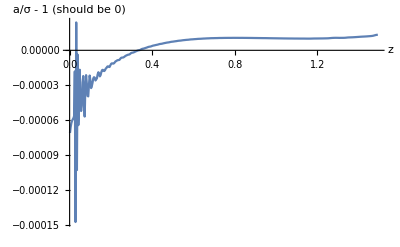

```mathematica
ph = Table[ϕtablez[[k]]//Interpolation,{k,1,nbz}];
dph[x_]=Table[D[ph[[k]][x],{x,1}],{k,1,nbz}];
tabledphi[k_]:=dph[ypts[k]][[k]];
varphi[k_] := ph[[k]][ypts[k]];

data[k_] := {Sign[ypts[k]]*Sqrt[2*(ypts[k]*tabledphi[k]-varphi[k])],tabledphi[k]}//Transpose;
degree=7;
basis=Table[x^k,{k,1,degree}];
zeta=Table[{Fit[data[n],basis,x]},{n,1,nbz}];

a = {Rpts,Table[D[zeta[[k,1]],{x,1}]/1!/.x->0,{k,1,nbz}]}//Transpose//Interpolation;
b = {Rpts,Table[D[zeta[[k,1]],{x,2}]/2!/.x->0,{k,1,nbz}]}//Transpose//Interpolation;
c = {Rpts,Table[D[zeta[[k,1]],{x,3}]/3!/.x->0,{k,1,nbz}]}//Transpose//Interpolation;
d = {Rpts,Table[D[zeta[[k,1]],{x,4}]/4!/.x->0,{k,1,nbz}]}//Transpose//Interpolation;
e = {Rpts,Table[D[zeta[[k,1]],{x,5}]/5!/.x->0,{k,1,nbz}]}//Transpose//Interpolation;
EffCollapse[x_,Ru_]=a[Ru]*x +b[Ru]*x^2 +c[Ru]*x^3 +d[Ru]*x^4 +e[Ru]*x^5;

(*A good sanity check since "a" is supposed to be the slice standard deviation*)
ListLinePlot[{zR[Rpts],a[Rpts]/Sqrt[sig2[Rpts*θ,zR[Rpts]]]-1}//Transpose,PlotRange->All,AxesLabel->{"z","a/σ - 1 (should be 0)"}]

(*Again, it is possible to save that*)
(*Export[FileNameJoin[{NotebookDirectory[],"EffCollapse.m"}],EffCollapse[x,Ru]]*)
```

## Joint CGF between 2 line-of-sight-projected variables (lengthy and un-optimised but working)

```mathematica
(*Optional cell, can be useful to clean everything and only load what is useful in the previous computations*)

ClearAll["Global`*"];

EffCollapse[x_,Ru_]= Import[FileNameJoin[{NotebookDirectory[],"EffCollapse.m"}]];

Omegam = 0.279;
Omegal = 1-Omegam;
H0 = 100;
c = 299792.458;

R = Import[FileNameJoin[{NotebookDirectory[],"distance.m"}]];
zR= Interpolation[Table[{NIntegrate[(c/H0)/Sqrt[Omegal+Omegam(1+zp)^3],{zp,0,z},PrecisionGoal->15],z},{z,0,6.,0.01}],InterpolationOrder->7];

Rsamp = 10; (*Samling of the line-of-sight in Mpc/h*)
Rs = R[1.5]; (*Arbitrary choice for a stopping point, just increase the value if your sources are higher in redshift*)
imax = (Rs+Rsamp*0.5)/Rsamp//IntegerPart; (*This makes sure that the last point is just below Rs*)
Rpts = Table[Rsamp*(i−0.5),{i,1,imax}];
Rweight = Table[Rsamp,{i,1,imax}];
nbz = imax
```

Let' s already compute the joint CGF for complex arguments since we have set up everything to that goal. The modifications to obtain the CGF in real space should be straightforward.

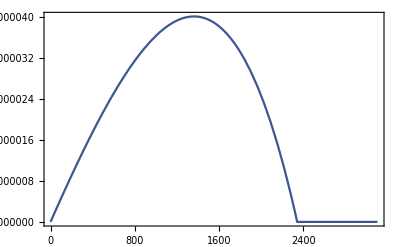
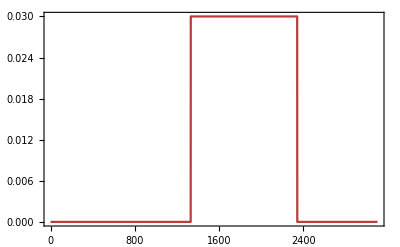

```mathematica
(*Let's define the two projection kernels. Here I'm looking at a kappa field at zs = 1 and a flat kernel 
for galaxies (one would more rigorously want a galaxy distribution) between z = 0.5 and 1. The linear bias can already be taken into account in the kernel.*)

c = 299792.458; (*needed because of a poor choice of names in the effective collapse parameters*)

b1 = 0.5;  (*Put in your desired (eulerian) linear galaxy bias value*)
F1[Ru_]=Piecewise[{{1.5*Omegam*(H0/c)^2*Ru*(R[1.]-Ru)/R[1.]*(1+zR[Ru]),zR[Ru]<=1.}}];
F2[Ru_]=b1*Piecewise[{{6*10^(-2),0.5<=zR[Ru]<=1.}}]; (*Chosen to get a std of order unity, really unrealistic*)

(*Let's visualise our 2 kernels*)
f=ColorData["DarkRainbow"];
plot1 = Plot[F1[r], {r,0,R[1.5]},PlotStyle -> f[0],ImagePadding -> 25,Frame -> {True, True, True, False},FrameStyle -> {Automatic, f[0], Automatic, Automatic},FrameLabel -> {{None, "Thing"}, {None, None}}];
plot2 = Plot[F2[r], {r,0,R[1.5]},PlotStyle -> f[1],ImagePadding -> 25,Frame -> {False, False, False, True},FrameTicks -> {{None, All}, {None, None}},FrameStyle -> {Automatic, Automatic, Automatic, f[1]},FrameLabel -> {{None, "Thing"}, {None, None}}];
Overlay[{plot1, plot2}]
```

Thanks to the series development of the (joint-)CGF, we know that for pure imaginary iλ values, we must have

```mathematica
ℜ[ϕ(-i Subscript[λ, 1],-i Subscript[λ, 2])]==ℜ[ϕ(i Subscript[λ, 1],i Subscript[λ, 2])]
```

and

```mathematica
ℑ[ϕ(-i Subscript[λ, 1],-i Subscript[λ, 2])]==-ℑ[ϕ(i Subscript[λ, 1],i Subscript[λ, 2])].
```

We thus only need to compute 2 quarters of the (λ1, λ2) plane if we perform, as in the 1D case, the inverse laplace transform along the imaginary axes.

```mathematica
(*ϕ(λ1,λ2) for λ1>0 & λ2>0 *) 

(*Given the difference in the order of magnitudes of the two variables (seen in their respective projection kernels), 
a good numerical sampling and range of λ values might be different for the two variables. 
To keep the formatting of the previous 1D computation and for simplicity, I thus apply a contraction factor fcont 
for the λ of the 2nd variable directly from the λ values of the 1st. Its value is very empirical, I estimated it playing around
with the 1D PDF of the 2nd variable (following the main sections of this notebook on the convergence PDF) and found that a ratio between the projection kernels
is a good value.*)

fcont = .001;
dzeta[tau_,Ru_] = D[EffCollapse[tau,Ru],{tau,1}];

Clear[deltaintermediate,ϕprojintermediatey]
ymax = 2000;
ymin = 0;
samp = 20;
ypts = I*Table[y,{y,ymin,ymax,samp}];

deltaintermediate[1,m_,k_]:=delta/.FindRoot[delta-dzeta[delta,Rpts[[k]]]*(ypts[[1]]*F1[Rpts[[k]]]+fcont*ypts[[m]]*F2[Rpts[[k]]]),{delta,I*(10^(-5))^.5},MaxIterations->1000];
nby=ypts//Length;
deltaintermediate[n_,m_,k_]:= deltaintermediate[n,m,k]= delta/.FindRoot[delta-dzeta[delta,Rpts[[k]]]*(ypts[[n]]*F1[Rpts[[k]]]+fcont*ypts[[m]]*F2[Rpts[[k]]]),{delta,deltaintermediate[n-1,m,k]},MaxIterations->1000];
deltapts = Transpose[Table[Table[Table[deltaintermediate[nn,mm,kk],{nn,1,nby}],{mm,1,nby}],{kk,1,nbz}],{3,2,1}];
ϕprojintermediatey[ni_,mi_]:= ϕprojintermediatey[ni,mi]= Total[Rweight*((ypts[[ni]]*Map[F1[#]&,Rpts]+fcont*ypts[[mi]]*Map[F2[#]&,Rpts])*EffCollapse[deltapts[[ni,mi]],Rpts]-deltapts[[ni,mi]]^2/2)];
Phi12 = Table[{ypts[[nn]],ypts[[mm]],ϕprojintermediatey[nn,mm]},{nn,1,nby},{mm,1,nby}]//Flatten[#,1]&;

(*Let's save that*)
(*Export[FileNameJoin[{NotebookDirectory[],"Phi12.m"}],Phi12]*)
```

```mathematica
(*ϕ(λ1,λ2) for λ1<0 & λ2>0 *)

Clear[deltaintermediate,ϕprojintermediatey]
ymax = 2000;
ymin = 0;
samp = 20;
ypts = I*Table[y,{y,ymin,ymax,samp}];

deltaintermediate[1,m_,k_]:=delta/.FindRoot[delta-dzeta[delta,Rpts[[k]]]*(-ypts[[1]]*F1[Rpts[[k]]]+fcont*ypts[[m]]*F2[Rpts[[k]]]),{delta,I*(10^(-5))^.5},MaxIterations->1000];
nby=ypts//Length;
deltaintermediate[n_,m_,k_]:= deltaintermediate[n,m,k]= delta/.FindRoot[delta-dzeta[delta,Rpts[[k]]]*(-ypts[[n]]*F1[Rpts[[k]]]+fcont*ypts[[m]]*F2[Rpts[[k]]]),{delta,deltaintermediate[n-1,m,k]},MaxIterations->1000];
deltapts = Transpose[Table[Table[Table[deltaintermediate[nn,mm,kk],{nn,1,nby}],{mm,1,nby}],{kk,1,nbz}],{3,2,1}];
ϕprojintermediatey[ni_,mi_]:= ϕprojintermediatey[ni,mi]= Total[Rweight*((-ypts[[ni]]*Map[F1[#]&,Rpts]+fcont*ypts[[mi]]*Map[F2[#]&,Rpts])*EffCollapse[deltapts[[ni,mi]],Rpts]-deltapts[[ni,mi]]^2/2)];
Phi12bis = Table[{-ypts[[nn]],ypts[[mm]],ϕprojintermediatey[nn,mm]},{nn,1,nby},{mm,1,nby}]//Flatten[#,1]&;

(*Let's save that*)
(*Export[FileNameJoin[{NotebookDirectory[],"Phi12bis.m"}],Phi12bis]*)
```

We now reconstruct the complete matrix of ϕ (iλ1, iλ2) (easier to reconstruct the PDF afterward)

```mathematica
PHI12=SortBy[Join[Re[Phi12]-I*Im[Phi12],Phi12,Re[Phi12bis]-I*Im[Phi12bis],Phi12bis]//DeleteDuplicates,{Im[#][[1]]&,Im[#][[2]]&}];

(*Let's save that*)
(*Export[FileNameJoin[{NotebookDirectory[],"PHI12.m"}],PHI12]*)
```

## Compute the individual and joint-PDFs

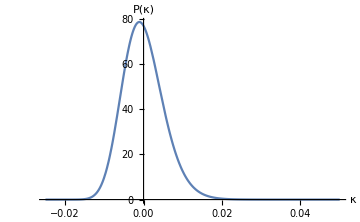
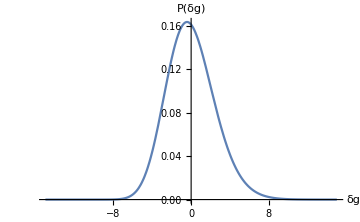

```mathematica
yweight=Append[Prepend[Table[samp I,{a,1,Length[ypts]-2}],samp/2 I],samp/2 I];

(*P(κ1) -> Obtain ϕ(λ1) from ϕ(λ1,λ2)*)
Clear[ephi,x2,x3,x4,h1,h2,h3]
x3=Fold[Partition,Flatten[Phi12],Most[Reverse[{nby,nby,3}]]]; (*This is just to put the CGF in the right format, mathematica shinanigans*)
x4 = Transpose[x3,{2,1}];
ephi = Exp[Transpose[x4[[1]]][[3]]];
h1[delta_] := h1[delta] = Total[yweight*Exp[-ypts*delta]*ephi/Pi] //Im//Abs;
gkappa = Interpolation[Table[{delta,h1[delta]},{delta,-0.08,0.25,.001}]];

(*P(κ2) -> Obtain ϕ(λ2) from ϕ(λ1,λ2)*)
Clear[ephi,x2,x3,x4,h1,h2,h3,h2bis]
x2=Fold[Partition,Flatten[Phi12],Most[Reverse[{nby,nby,3}]]];
ephi2 = Exp[Transpose[x2[[1]]][[3]]];
h2[delta_] := h2[delta] = Total[fcont*yweight*Exp[-fcont*ypts*delta]*ephi2/Pi] //Im//Abs;
gkappa2 = Interpolation[Table[{delta,h2[delta]},{delta,-15,15,.1}]];

{Plot[gkappa[x],{x,-0.025,0.05},AxesLabel->{"κ","P(κ)"},ImageSize->Medium],Plot[gkappa2[x],{x,-15,15},AxesLabel->{"δg","P(δg)"},ImageSize->Medium]}
```

```mathematica
yptsbis = I*Table[y,{y,-ymax,ymax,samp}];
yweightbis=Append[Prepend[Table[samp I,{a,1,Length[yptsbis]-2}],samp/2 I],samp/2 I];
nbybis = yptsbis//Length;

(*P(κ1,κ2)*)
Clear[x2,A,kpts1,kpts2,U,V,ans2]
x2 = Fold[Partition,Transpose[PHI12][[3]],Most[Reverse[{nbybis,nbybis}]]];
A = Exp[x2]/Pi^2/4;
kpts1 = Table[d1,{d1,-0.08,0.25,.001}];
kpts2 = Table[d2,{d2,-15,15,.1}];
U = Exp[-KroneckerProduct[kpts1, yptsbis]].DiagonalMatrix[SparseArray[yweightbis]];
V = fcont*yweightbis Exp[-KroneckerProduct[fcont*yptsbis, kpts2]];
ans2 = U.A.V;

gkappa12 =Interpolation[Table[{kpts1[[i]],kpts2[[j]],ans2[[i,j]]//Re//Abs},{i,1,kpts1//Length},{j,1,kpts2//Length}]//Flatten[#,1]&];
Plot3D[gkappa12[x,y],{x,-0.025,0.025},{y,-15,15},PlotRange->All,AxesLabel->{"κ","δg","P(κ,δg)"},PlotPoints->50,ColorFunction->"DarkRainbow",Mesh->None]

(*A slower alternative in bad mathematica formatting, but easier to read*)
(*h1[delta1_,delta2_] := h1[delta1,delta2] = ((yweightbis*Exp[-yptsbis*delta1]).(Exp[x2]/Pi^2/4)).(yweightbis*Exp[-yptsbis*delta2])//Re//Abs;
gkappa12 = Interpolation[ParallelTable[{delta1,delta2,h1[delta1,delta2]},{delta1,-0.08,0.25,.001},{delta2,-15,15,.1}]//Flatten[#,1]&];*)
```

-Graphics3D-

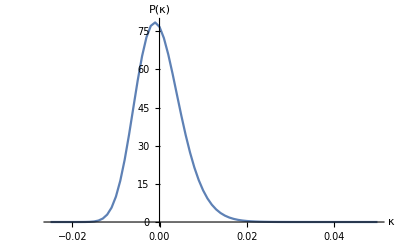

```mathematica
(*Let's check that we recover the correct individual PDF from the joint*)
gkap = Table[{k,NIntegrate[gkappa12[k,d],{d,-15,15}]},{k,-0.025,0.05,.001}];
ListLinePlot[gkap,PlotRange->All,AxesLabel->{"κ","P(κ)"}]
```

## III) Correcting the non-linear variance along the line-of-sight for Kaiser-Squires reconstructed fields

As described in arXiv:2307.09468, the reconstruction of the convergence field from an observed shear field under a mask leads to differences between the “true” underlying convergence and the reconstructed one. We thus need to model this reconstruction in order for our PDF models to be accurate. In the context of the large-deviations formalism, taking the mask into account can be translated in a simple modification of the non-linear variance at the different physical scales (for one chosen angular scale) along the line of sight. This applies directly to the two previous sections (the 1-pt convergence PDF and joint PDFs along the line of sight) and could straightforwardly be modified to the aperture mass section though there would virtually no reason to do so since the aperture mass can be reconstructed from the shear directly.

More formally, before jumping to the actual implementation, remember the 2D slice CGF at scale R and redshift z is given by the Legendre transform of the rate function ψ. The masking effects are taken into account by replacing the non-linear variance in its expression:

```mathematica
Subscript[ψ, (R,z)](δ)==1/2(τ(δ)^2 Subscript[σ, l]^2(R))/(Subscript[σ, l]^2(R[1+δ]^(1/2)))1/(Subscript[σ, nl]^2(R,z))->1/2(τ(δ)^2 Subscript[σ, l]^2(R))/(Subscript[σ, l]^2(R[1+δ]^(1/2)))1/(Subscript[σ, nl,masked]^2(R,z))
```

As a consequence, I here just implement the new masked variance along the line of sight for a given angular scale and computing whatever PDFs from that would just account to replacing the functions “sig2” which gave the usual non-linear variance in the previous sections by what we now compute.

```mathematica
(*First we load the pre-computed E to E modes mixing matrix. It only depends on the survey mask, here we have the mask of the DES Y3 survey from l=0 to l=3071*)
MEraw = Import[FileNameJoin[{NotebookDirectory[],"ME_DES_1024_lmax3071.dat"}]];
ME = MEraw[[3;;,3;;]]; (*We only need the matrix from l=2 because of the mass-sheet degeneracy*)

θ = 0.00581776; (*20 arcmin*)

(*We first load the non-linear power spectrum obtained with Class*)
ks=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/dataconfig_ks.dat"}],Number,RecordLists->True]//Flatten;
{kmini,kmaxi}={ks[[1]],ks[[-1]]};
zss=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/dataconfig_zs.dat"}],Number,RecordLists->True]//Flatten;
pks=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/fiducial_pks_nl_mm.dat"}],Number,RecordLists->True];
nbz = zss//Length;
nby = ks//Length;

(*We interpolate the power spectrum*)
Pk=Table[{{zss[[a]],ks[[b]]},pks[[a,b]]},{a,1,nbz},{b,1,nby}]//Flatten[#,1]&//Interpolation;

Wsh[l_]=(LegendreP[l-1,Cos[θ]]-LegendreP[l+1,Cos[θ]])/(2*l+1)/(1-Cos[θ]); (*top-hat filter in spherical-harmonics space*)
fl[l_]=(l+2)*(l-1)/l/(l+1); (*factor to go from convergence to shear*)
fsky = 0.11741690517468692;  (*tailored f_sky measured in data to recover correct smoothed projected variance: very close to the true survey f_sky*)

(*We define the 2D slice masked non-linear variance at scale R(z)θ and redshift z.*)
sigm2[z_]:=(ME.Table[Pk[z,lp/R[z]]*fl[lp]/(1+(lp/(1.6*1024))^2),{lp,2,3071}])*Table[(2*l+1)/4/Pi*Wsh[l]^2/fl[l]/R[z]^2,{l,2,3071}]/fsky//Total;

(*We compute the variance at fixed redshift values and interpolate the result*)
sig2=Table[{R[z],sigm2[z]},{z,0.0103,3.5,0.005}]//Interpolation;
```

## IV) Observational systematics in the modelling

To be added (see arXiv:2307.09468)

## V) Beyond Top-hat filters

To be added (see  arXiv:1708.00252)

## VI) The Aperture mass PDF

If you use this part, please cite : “Probability distribution function of the aperture mass field with large deviation theory” ( https://doi.org/10.1093/mnras/stab818 ) by Alexandre Barthelemy, Sandrine Codis & Francis Bernardeau.

```mathematica
ClearAll["Global`*"];
```

## Non - linear "2D covariance" along the line-of-sight

Compared to the above “variance along the line of sight”, we now need to compute the whole covariance between any two scales which greatly increases the computation time and file size due to the increased number of points. I have thus computed it in a better suited language and I just give the equivalent Mathematica code for completeness.  I have saved the cell product and we can use it for some top-hat radii combination and any lensing/projection kernel. I would suggest only using the  non-linear covariances I’m giving with the notebook, and if needed recompute them in a more suited programming language and/or on a computer cluster.

#### non - linear matter power spectrum (uncomment to run)

```mathematica
(*
(*We first load the non-linear power spectrum obtained with Class*)
ks=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/dataconfig_ks.dat"}],Number,RecordLists->True]//Flatten;
{kmini,kmaxi}={ks[[1]],ks[[-1]]};
zss=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/dataconfig_zs.dat"}],Number,RecordLists->True]//Flatten;
pks=ReadList[FileNameJoin[{NotebookDirectory[],"Power spectra/fiducial_pks_nl_mm.dat"}],Number,RecordLists->True];
nbz = zss//Length;
nby = ks//Length;

(*We interpolate the power spectrum*)
Pk=Table[{{zss[[a]],ks[[b]]},pks[[a,b]]},{a,1,nbz},{b,1,nby}]//Flatten[#,1]&//Interpolation;

(*We define the 2D top-hat function in fourier space*)
W[l_]=2 BesselJ[1,l]/(l);

(*We define the covariance at redshift z between two concentric 2D slices of radius R1 and R2*)
ssigma2[R1_,R2_,z_]:=NIntegrate[Pk[z,k] k W[k*R1]*W[k*R2],{k,kmini,kmaxi},Method->{"GlobalAdaptive","SymbolicProcessing"->0,"MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->16,PrecisionGoal->7,AccuracyGoal->Infinity]/2/Pi //Quiet;

(*For evaluation time, file size and loading time after having saved it, we only compute the covariance at scales R2 equal to either R1 or 2*R1.
This restricts the possible aperture mass filter configurations that can be evaluated and leads to some inaccuracies but this is straighforward to change if needed 
and is fine for illustrative purposes*)
(*The range of R values needs to be adapted to the redshift of sources and chosen angular top-hat radii*)
sigm2=ParallelTable[{{R1,R2,z},ssigma2[R1,R2,z]},{R1,0.0001,30,0.025},{R2,{0.0001,30,0.025}},{z,0,2,0.25}]//Flatten[#,2]&;

(*Since this entire cell operation is lengthy and only depends on the cosmology, we can save it and re-use it later*)
sig2=sigm2//Interpolation;
cov[r1_,r2_,z_]=sig2[r1,r2,z];
DumpSave[FileNameJoin[{NotebookDirectory[],"covariance_nl.mx"}],cov];
*)
```

## Aperture mass cumulants following Appendix C of arXiv:2012.03831

### Analytical forms of joint-cumulants in concentric long cylinders/2D slices

```mathematica
ClearAll["Global`*"]

(*The spherical collapse functional. One could replace it by its taylor expansion to make the angular-averaged PT kernels 
appear formally and obtain the tree-order results*)
τ[y_]=y^(-1/ν) (-1+y^(1/ν)) ν;

(*Everything will be computed from the second derivatives (Hessian) of the 2-variables rate function*)
detsig2[δ1_,δ2_,R1_,R2_,z_]=sig2[(1+δ1)^(1/2)*R1,(1+δ1)^(1/2)*R1,z]*sig2[(1+δ2)^(1/2)*R2,(1+δ2)^(1/2)*R2,z]-sig2[(1+δ1)^(1/2)*R1,(1+δ2)^(1/2)*R2,z]^2;
ψ[δ1_,δ2_,R1_,R2_,z_]=1/2/detsig2[δ1,δ2,R1,R2,z]*(sig2[(1+δ2)^(1/2)*R2,(1+δ2)^(1/2)*R2,z]*τ[1+δ1]^2 + sig2[(1+δ1)^(1/2)*R1,(1+δ1)^(1/2)*R1,z]*τ[1+δ2]^2 - 2*sig2[(1+δ1)^(1/2)*R1,(1+δ2)^(1/2)*R2,z]*τ[1+δ1]*τ[1+δ2]);
dψ11[δ1_,δ2_,R1_,R2_,z_]=D[ψ[δ1,δ2,R1,R2,z],{δ1,2}];
dψ22[δ1_,δ2_,R1_,R2_,z_]=D[ψ[δ1,δ2,R1,R2,z],{δ2,2}];
dψ12[δ1_,δ2_,R1_,R2_,z_]=D[ψ[δ1,δ2,R1,R2,z],{δ1,1},{δ2,1}];

(*We define the differential operators D1 and D2*)
D1[d1_,d2_,R1_,R2_,z_]=(dψ22[d1,d2,R1,R2,z]/(dψ11[d1,d2,R1,R2,z]*dψ22[d1,d2,R1,R2,z]-dψ12[d1,d2,R1,R2,z]^2)*D[#,{d1,1}]-dψ12[d1,d2,R1,R2,z]/(dψ11[d1,d2,R1,R2,z]*dψ22[d1,d2,R1,R2,z]-dψ12[d1,d2,R1,R2,z]^2)D[#,{d2,1}])&;
D2[d1_,d2_,R1_,R2_,z_]=(-dψ12[d1,d2,R1,R2,z]/(dψ11[d1,d2,R1,R2,z]*dψ22[d1,d2,R1,R2,z]-dψ12[d1,d2,R1,R2,z]^2)*D[#,{d1,1}]+dψ11[d1,d2,R1,R2,z]/(dψ11[d1,d2,R1,R2,z]*dψ22[d1,d2,R1,R2,z]-dψ12[d1,d2,R1,R2,z]^2)D[#,{d2,1}])&;

(*We here compute cumulants of order 3 (in d1=d2=0) but the higher-order ones are obtained by successively applying D1 and D2*)
k21[d1_,d2_,R1_,R2_,z_]=D1[d1,d2,R1,R2,z][-dψ12[d1,d2,R1,R2,z]/(dψ11[d1,d2,R1,R2,z]*dψ22[d1,d2,R1,R2,z]-dψ12[d1,d2,R1,R2,z]^2)];
k12[d1_,d2_,R1_,R2_,z_]=D2[d1,d2,R1,R2,z][-dψ12[d1,d2,R1,R2,z]/(dψ11[d1,d2,R1,R2,z]*dψ22[d1,d2,R1,R2,z]-dψ12[d1,d2,R1,R2,z]^2)];

(*We also need the 1-variable 3rd cumulant more easily defined outside of the previous expressions even though its expression is formally contained above*)
Psicyl[δ_,R_,z_]=1/2*τ[1+δ]^2/sig2[(1+δ)^(1/2)*R,(1+δ)^(1/2)*R,z];
dPsicyl2[d_,R_,z_] =D[Psicyl[d,R,z],{d,2}];
k3[d_,R_,z_]= 1/dPsicyl2[d,R,z]*D[1/dPsicyl2[d,R,z],{d,1}];

(*We obtain the final expressions for each cumulant which we also combine to obtain the 3rd cumulant of 1 disk minus the other*)
K3[R_,z_]=k3[0,R,z]//FullSimplify//Expand;
K12[R1_,R2_,z_]=k12[0,0,R1,R2,z]//FullSimplify//Expand;
K21[R1_,R2_,z_]=k21[0,0,R1,R2,z]//FullSimplify//Expand;
K3slice[R1_,R2_,z_]= k3[0,R2,z] - k3[0,R1,z] + 3*k21[0,0,R1,R2,z] - 3*k12[0,0,R1,R2,z]//FullSimplify//Expand;
Print["<Map^3>_c = ∫ dχ ω(χ)^3 × (",K3slice[R1,R2,z],")"]
```

<Map^3>_c = ∫ dχ ω(χ)^3 × (-3 sig2[R1,R1,z]^2-(3 sig2[R1,R1,z]^2)/ν+6 sig2[R1,R1,z] sig2[R1,R2,z]+(6 sig2[R1,R1,z] sig2[R1,R2,z])/ν-6 sig2[R1,R2,z] sig2[R2,R2,z]-(6 sig2[R1,R2,z] sig2[R2,R2,z])/ν+3 sig2[R2,R2,z]^2+(3 sig2[R2,R2,z]^2)/ν-3/2 R1 sig2[R1,R1,z] sig2^(0,1,0)[R1,R1,z]+3/2 R1 sig2[R1,R2,z] sig2^(0,1,0)[R1,R1,z]+3 R2 sig2[R1,R2,z] sig2^(0,1,0)[R1,R2,z]-3 R2 sig2[R2,R2,z] sig2^(0,1,0)[R1,R2,z]-3/2 R2 sig2[R1,R2,z] sig2^(0,1,0)[R2,R2,z]+3/2 R2 sig2[R2,R2,z] sig2^(0,1,0)[R2,R2,z]-3/2 R1 sig2[R1,R1,z] sig2^(1,0,0)[R1,R1,z]+3/2 R1 sig2[R1,R2,z] sig2^(1,0,0)[R1,R1,z]+3 R1 sig2[R1,R1,z] sig2^(1,0,0)[R1,R2,z]-3 R1 sig2[R1,R2,z] sig2^(1,0,0)[R1,R2,z]-3/2 R2 sig2[R1,R2,z] sig2^(1,0,0)[R2,R2,z]+3/2 R2 sig2[R2,R2,z] sig2^(1,0,0)[R2,R2,z])

### Projected cumulants along the line-of-sight

```mathematica
(*Define the variance of 1 disk minus the other in 1 2D slice*)
sig2slice[Ru1_,Ru2_,z_]=sig2[Ru1,Ru1,z]+sig2[Ru2,Ru2,z]-2*sig2[Ru1,Ru2,z];

(*Import the previously computed non-linear covariance between two concentric 2D cells*)
Get[FileNameJoin[{NotebookDirectory[],"halofit_covariance.mx"}]];
sig2[r1_,r2_,z_]=cov[r1,r2,z]

(*Define the chosen flat cosmology and comoving distances*)
ν = 1.4;
Omegam = 0.279;
Omegal = 1-Omegam;
H0 = 100; (*Forces units to Mpc/h. If you edit this notebook make sure that everything is still consistent with that choice.*)
c = 299792.458;
R = Import[FileNameJoin[{NotebookDirectory[],"distance.m"}]];
zR= Interpolation[Table[{NIntegrate[(c/H0)/Sqrt[Omegal+Omegam(1+zp)^3],{zp,0,z},PrecisionGoal->15],z},{z,0,6.,0.01}],InterpolationOrder->2];

(*Let's define the convergence projection kernel. 
Remember that we define the aperture mass as the difference between two top-hat smoothing scales of the convergence field.
As before, taking into account source distribution is done only by changing this kernel, see an example in the BNT transform section of this notebook*)
F[z_,zs_]:=Piecewise[{{1.5*Omegam*(H0/c)^2*R[z]*(R[zs]-R[z])/R[zs]*(1+z),z<=zs}}];
```

InterpolatingFunction[{{0.0001, 29.9751}, {0.0001, 29.9751}, {0., 2.}}, <>][r1,r2,z]

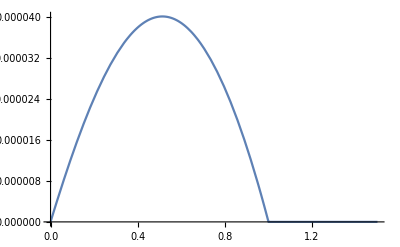

```mathematica
Plot[F[z,1],{z,0,1.5},PlotRange->All]
```

```mathematica
(*As an example, let's compute the line-of-sight projection to obtain the two-cells joint convergence cumulants up to order 3, 
as well as the aperture mass variance and skewness*)

zs = 1.0334;

t1 = 0.00290888;  (*10 arcmin*)
t2 = t1*2;

zmin = 10^-4;
zmax = zs;
zsamp = 0.05;
zpts = Table[z,{z,zmin,zmax,zsamp}];
zweight = Prepend[Append[Table[zsamp,{a,1,Length[zpts]-2}],zsamp/2],zsamp/2];

K2Map=Total[zweight*Map[F[#,zs]&,zpts]^2*sig2slice[R[zpts]*t1,R[zpts]*t2,zpts]*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];
K2kappa1=Total[zweight*Map[F[#,zs]&,zpts]^2*sig2[R[zpts]*t1,R[zpts]*t1,zpts]*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];
K2kappa2=Total[zweight*Map[F[#,zs]&,zpts]^2*sig2[R[zpts]*t2,R[zpts]*t2,zpts]*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];

K3Map=Total[zweight*Map[F[#,zs]&,zpts]^3*K3slice[R[zpts]*t1,R[zpts]*t2,zpts]*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];
K3kappa1=Total[zweight*Map[F[#,zs]&,zpts]^3*K3[R[zpts]*t1,zpts]*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];
K3kappa2=Total[zweight*Map[F[#,zs]&,zpts]^3*K3[R[zpts]*t2,zpts]*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];
K3kappa21=Total[zweight*Map[F[#,zs]&,zpts]^3*K21[R[zpts]*t1,R[zpts]*t2,zpts]*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];
K3kappa12=Total[zweight*Map[F[#,zs]&,zpts]^3*K12[R[zpts]*t1,R[zpts]*t2,zpts]*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];
```

```mathematica
Print["σ^2_Map= ",K2Map]
Print["S3_Map= ",K3Map/K2Map^2]
Print["σ^2_κ1= ",K2kappa1]
Print["S3_κ1= ",K3kappa1/K2kappa1^2]
Print["σ^2_κ2= ",K2kappa2]
Print["S3_κ2= ",K3kappa2/K2kappa2^2]
Print["<κ1^2 κ2>= ",K3kappa21]
Print["<κ1 κ2^2>= ",K3kappa12]
```

σ^2_Map= 0.0000142796

S3_Map= -70.9651

σ^2_κ1= 0.0000507704

S3_κ1= 73.7509

σ^2_κ2= 0.0000290242

S3_κ2= 72.5814

<κ1^2 κ2>= 1.10939×10^-7

<κ1 κ2^2>= 7.27758×10^-8

## Aperture mass Cumulant Generating Function along the line-of-sight (working but not fully optimised)

```mathematica
ClearAll["Global`*"];

τ[y_]=y^(-1/ν)*(-1+y^(1/ν))*ν;
R = Import[FileNameJoin[{NotebookDirectory[],"distance.m"}]];

sig2slice[Ru1_,Ru2_,z_]=sig2[Ru1,Ru1,z]+sig2[Ru2,Ru2,z]-2*sig2[Ru1,Ru2,z];

detsig2[δ1_,δ2_,R1_,R2_,z_]=sig2[(1+δ1)^(1/2)*R1,(1+δ1)^(1/2)*R1,z]*sig2[(1+δ2)^(1/2)*R2,(1+δ2)^(1/2)*R2,z]-sig2[(1+δ1)^(1/2)*R1,(1+δ2)^(1/2)*R2,z]^2;
ψ[δ1_,δ2_,R1_,R2_,z_]=1/2/detsig2[δ1,δ2,R1,R2,z]*(sig2[(1+δ2)^(1/2)*R2,(1+δ2)^(1/2)*R2,z]*τ[1+δ1]^2 + sig2[(1+δ1)^(1/2)*R1,(1+δ1)^(1/2)*R1,z]*τ[1+δ2]^2 - 2*sig2[(1+δ1)^(1/2)*R1,(1+δ2)^(1/2)*R2,z]*τ[1+δ1]*τ[1+δ2]);

dψ1[δ1_,δ2_,R1_,R2_,z_]=D[ψ[δ1,δ2,R1,R2,z],{δ1,1}]//Simplify;
dψ2[δ1_,δ2_,R1_,R2_,z_]=D[ψ[δ1,δ2,R1,R2,z],{δ2,1}]//Simplify;

dψ11[δ1_,δ2_,R1_,R2_,z_]=D[ψ[δ1,δ2,R1,R2,z],{δ1,2}];
dψ22[δ1_,δ2_,R1_,R2_,z_]=D[ψ[δ1,δ2,R1,R2,z],{δ2,2}];
dψ12[δ1_,δ2_,R1_,R2_,z_]=D[ψ[δ1,δ2,R1,R2,z],{δ1,1},{δ2,1}];

Omegam = 0.279;
Omegal = 1-Omegam;
H0 = 100; (*Forces units to Mpc/h. If you edit this notebook make sure that everything is still consistent with that choice.*)
c = 299792.458;
ν = 1.4;

(*Import the previously computed non-linear covariance between two concentric 2D cells*)
Get[FileNameJoin[{NotebookDirectory[],"halofit_covariance.mx"}]];
sig2[r1_,r2_,z_]=cov[r1,r2,z]

zs = 1.0334;
F[z_]:=F[z]=1.5*Omegam*(H0/c)^2*R[z]*(R[zs]-R[z])/R[zs]*(1+z);

t1 = 0.00290888;
t2 = t1*2;

cfgenerator=Compile[{delta1,delta2,R1,R2,z},#,RuntimeOptions->"EvaluateSymbolically"->False]&;
{cf1,cf2,cf3}=cfgenerator/@{dψ1[delta1,delta2,R1,R2,z],dψ2[delta1,delta2,R1,R2,z],dψ11[delta1,delta2,R1,R2,z]*dψ22[delta1,delta2,R1,R2,z]-dψ12[delta1,delta2,R1,R2,z]^2};
```

InterpolatingFunction[{{0.0001, 29.9751}, {0.0001, 29.9751}, {0., 2.}}, <>][r1,r2,z]

```mathematica
(*An example of why we do some pre-compilation*)
{delta1,delta2}/.FindRoot[dψ1[delta1,delta2,R[0.5]*t1,R[0.5]*t2,0.5] == -10*F[0.5] && dψ2[delta1,delta2,R[0.5]*t1,R[0.5]*t2,0.5] == 10*F[0.5],{delta1,0,-0.99,6.},{delta2,0,-0.99,6.}]//AbsoluteTiming

{delta1,delta2}/.FindRoot[cf1[delta1,delta2,R[0.5]*t1,R[0.5]*t2,0.5]==-10*F[0.5] &&cf2[delta1,delta2,R[0.5]*t1,R[0.5]*t2,0.5]==10*F[0.5] ,{delta1,0,-0.9999,6.1},{delta2,0,-0.9999,6.1}]//AbsoluteTiming
```

{18.115,{-0.0025599,-0.000547795}}

{0.760255,{-0.0025599,-0.000547795}}

### [Optional] Estimation of the two critical points

Similarly to the convergence CGF calculation, there exists some critical values of λ along the line of sight for which the two-cell rate function is not convex anymore. For multiple cells statistics, this is no longer just a single value but rather a line in how many dimensions than there are cells. For the aperture mass , we are looking at a two-cell critical line but where we impose λ = λ2 = -λ1. This thus leads to the aperture mass CGF having two critical values (the intersection of the y = -x curve and the two-cell critical line) which one would typically like to roughly estimate to choose accurate boundaries in the CGF implementation.  Similarly to the convergence computation, we estimate the aperture-mass critical values by computing them along the line of sight in each 2D slice, re-weighting them by the lensing/projection kernel, and taking the smallest values.

Let me start by illustrating how the procedure work . We plot the contours* for which the determinant of the hessian of the rate function is 0 in black . This gives us the two-cell critical line in {δ1, δ2}  coordinates . I then overplot in red the λ1 (δ1, δ2) + λ2 (δ1, δ2) = 0 line. The two intersections correspond to the two critical values in {δ1, δ2}  coordinates for the slice at the chosen redshift .

*the contours are noisy because we want a fast evaluation and do not care much about what happens outside of the first zero crossings. We get away with this by looking at the crossings closest to (0,0) here shown as a blue cross.

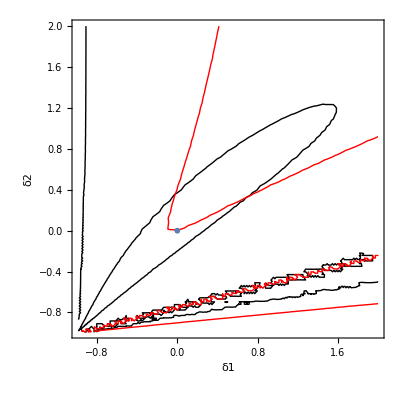

```mathematica
z = 0.05;
Show[ContourPlot[cf3[d1,d2,R[z]*t1,R[z]*t2,z],{d1,-0.99,2},{d2,-0.99,2},Contours->{0},ContourShading->None,FrameLabel->{"δ1","δ2"}],ContourPlot[cf1[d1,d2,R[z]*t1,R[z]*t2,z]+cf2[d1,d2,R[z]*t1,R[z]*t2,z],{d1,-0.99,2},{d2,-0.99,2},Contours->{0},ContourShading->None,ContourStyle->Red],ListPlot[{{0,0}}, PlotMarkers -> Style["✚", Small]]]
```

I then translate the above plot in {λ1,λ2} coordinates re-scaled by the lensing kernel so that these are the actual values I want to compare along the line of sight. Mathematica finds the intersections “graphically”. I loop over the procedure for a few redshifts from the observer to the sources and thus find the projected critical values. For illustration purposes I have already identified the redshift values close to the minimum critical lambdas.

z = 0.05

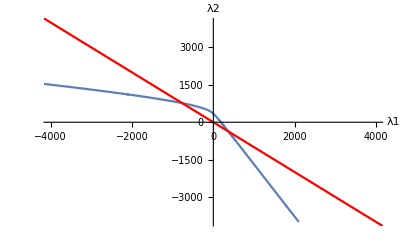

The two critical λ at this z are: {765.107,-367.964}

z = 0.1

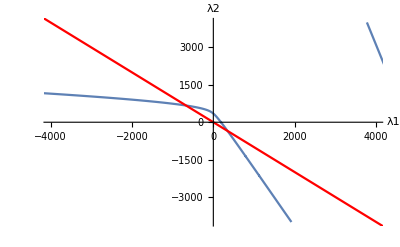

The two critical λ at this z are: {669.539,-348.12}

z = 0.15

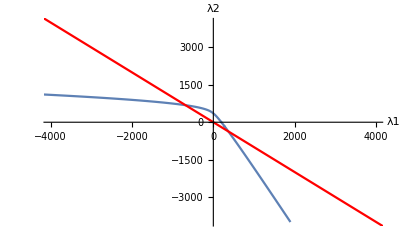

The two critical λ at this z are: {682.27,-368.921}

```mathematica
For[i=1,i<=3,i++,
z = i*0.05;
d=Cases[Normal@ContourPlot[cf3[d1,d2,R[z]*t1,R[z]*t2,z],{d1,-0.99,2},{d2,-0.99,2},Contours->{0},ContourShading->None],Line[pts_]->pts,Infinity]//Flatten[#,1]&//Transpose;
l = {Thread[cf1[d[[1]],d[[2]],R[z]*t1,R[z]*t2,z]//Quiet]/F[z],Thread[cf2[d[[1]],d[[2]],R[z]*t1,R[z]*t2,z]//Quiet]/F[z]}//Transpose;
pl = Show[ListLinePlot[l,PlotRange->{{-4000,4000},{-4000,4000}},AxesLabel->{"λ1","λ2"}],Plot[-x,{x,-5000,5000},PlotStyle->Red]];
Print["z = ",z];
Print[pl];
Print["The two critical λ at this z are: ",Transpose[Cases[Graphics`Mesh`FindIntersections@pl,x_/;x[[1]]==-x[[2]]]][[2]]]]
```

Looking at the results, it seems that a good guess for the two critical points of the aperture mass CGF for the chosen zs and {t1,t2} is close to ~660 and ~340. Just to be safe, I thus choose ymax to be 600 and ymin to be -300.

### Actual CGF computation

{{-300,0.758128},{-265,0.574208},{-230,0.42169},{-195,0.296446},{-160,0.195677},{-125,0.117336},{-90,0.0598633},{-55,0.0220355},{-20,0.00287582},{15,0.0015985},{50,0.0175702},{85,0.0502835},{120,0.099338},{155,0.164428},{190,0.245331},{225,0.341909},{260,0.454095},{295,0.581905},{330,0.725432},{365,0.884856},{400,1.06045},{435,1.25262},{470,1.46188},{505,1.68895},{540,1.93478},{575,2.20069}}

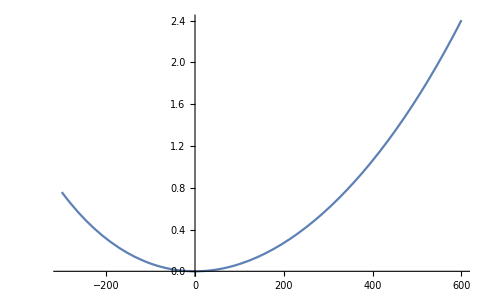

```mathematica
(*With default values, this takes roughly 5-10 minutes*)

zmin = 10^(-4);
zmax = zs;
zsamp = 0.05;
zpts = Table[z,{z,zmin,zmax,zsamp}];
zweight = Prepend[Append[Table[zsamp,{a,1,Length[zpts]-2}],zsamp/2],zsamp/2];

ymax = 600;
ymin = -300;
samp = 35;
ypts = Table[y,{y,ymin,ymax,samp}];

nby=ypts//Length;
nbz=zpts//Length;

Clear[deltaintermediate]
deltaintermediate[1,k_]:={delta1,delta2}/.FindRoot[cf1[delta1,delta2,R[zpts[[k]]]*t1,R[zpts[[k]]]*t2,zpts[[k]]] == -ypts[[1]]*F[zpts[[k]]] && cf2[delta1,delta2,R[zpts[[k]]]*t1,R[zpts[[k]]]*t2,zpts[[k]]] == ypts[[1]]*F[zpts[[k]]],{delta1,0,-0.9999,6.1},{delta2,0,-0.9999,6.1}];
deltaintermediate[n_,k_]:= deltaintermediate[n,k]= {delta1,delta2}/.FindRoot[cf1[delta1,delta2,R[zpts[[k]]]*t1,R[zpts[[k]]]*t2,zpts[[k]]] == -ypts[[n]]*F[zpts[[k]]] && cf2[delta1,delta2,R[zpts[[k]]]*t1,R[zpts[[k]]]*t2,zpts[[k]]] == ypts[[n]]*F[zpts[[k]]],{delta1,deltaintermediate[n-1,k][[1]],-0.9999,6.1},{delta2,deltaintermediate[n-1,k][[2]],-0.9999,6.1}];

d1pts = Table[Table[deltaintermediate[nn,kk][[1]],{nn,1,nby}],{kk,1,nbz}]//Transpose;
d2pts = Table[Table[deltaintermediate[nn,kk][[2]],{nn,1,nby}],{kk,1,nbz}]//Transpose;

ϕprojintermediatey[ni_]:= ϕprojintermediatey[ni]= Total[zweight*(ypts[[ni]]*F[zpts]*(d2pts[[ni]]-d1pts[[ni]])-ψ[d1pts[[ni]],d2pts[[ni]],R[zpts]*t1,R[zpts]*t2,zpts])*(c/H0)/Sqrt[Omegal+Omegam*(1+zpts)^3]];
ϕprojy = Table[ϕprojintermediatey[nn],{nn,1,nby}];

Phi = Interpolation[{ypts,ϕprojy}//Transpose,InterpolationOrder->3];
Phi2 = {ypts,ϕprojy}//Transpose
Show[Plot[Phi[y],{y,ymin,ymax}]]
```

The CGF is an observable on its own but we can still use it to compute the PDF

## Computation of the PDF from the effective collapse approach (see section 2.6 in this paper for details)

```mathematica
ph = Phi2//Interpolation;
dph[x_]=D[ph[x],{x,1}];
tabledph=dph[ypts];
varphi= ph[ypts];

data= {Sign[ypts]*Sqrt[2*(ypts*tabledph-varphi)],tabledph}//Transpose;
degree=7;
basis=Table[x^k,{k,1,degree}];
zetabis=Fit[data,basis,x]
zeta[x_]=zetabis;
```

0.00377888 x-0.000168929 x^2+0.0000539742 x^3-3.54398×10^-6 x^4+1.28518×10^-6 x^5-3.50921×10^-7 x^6+8.44274×10^-8 x^7

```mathematica
(*Check that the first term squared gives back the variance*)
0.0037788792616428074^2
```

0.0000142799

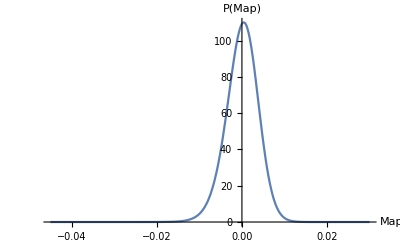

```mathematica
dzeta[t_]=D[zeta[t],{t,1}];

Clear[tauintermediate,taupts,ephi,h,geff];
ymax =4000.;
ymin = 0;
samp=20;
ypts = I*Table[y,{y,ymin,ymax,samp}];

(*The values of ypts might need to be adjusted depending on the computed PDF. 
Plot the imaginary part of yweight*Exp[-ypts*delta]*ephi/Pi for different values of delta (the convergence values) and 
make sure that the sampling and max values are good enough to capture the oscillations and their damping*)

yweight=Append[Prepend[Table[samp I,{a,1,Length[ypts]-2}],samp/2 I],samp/2 I];
nby=ypts//Length;
tauintermediate[1]=tau/.FindRoot[tau-dzeta[tau]*ypts[[1]],{tau,(I 10^(-5))^.5},MaxIterations->1000];
tauintermediate[n_]:= tauintermediate[n]= tau/.FindRoot[tau-dzeta[tau]*ypts[[n]],{tau,tauintermediate[n-1]},MaxIterations->1000];
taupts =Table[tauintermediate[nn],{nn,1,nby}];
ephi= Exp[ypts*zeta[taupts]-taupts^2/2];
h[delta_] := h[delta] = Total[yweight*Exp[-ypts*delta]*ephi/Pi] //Im;
geff = Interpolation[Table[{delta,h[delta]},{delta,-0.08,0.25,.001}]];

Plot[geff[x],{x,-0.045,0.03},AxesLabel->{"Map","P(Map)"},PlotRange->All]
```

```mathematica
(*Let's check that we recover the correct variance and skewness as a check that the integration was succesful*)
NIntegrate[x^2*geff[x],{x,-0.045,0.03}]-(NIntegrate[x*geff[x],{x,-0.045,0.03}])^2
NIntegrate[x^3*geff[x],{x,-0.045,0.03}]/NIntegrate[x^2*geff[x],{x,-0.045,0.03}]^2
```

0.0000142799

-70.9789

We nicely recover the values that we computed with the cumulants formulas !